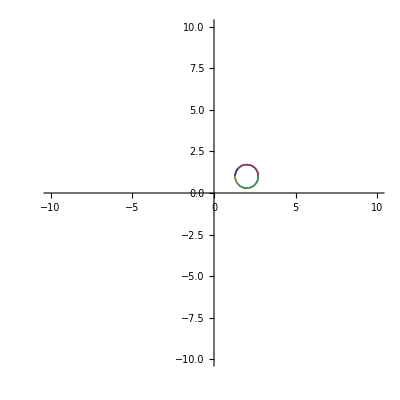

```mathematica
Clear["Global`*"];
(*Define the Following;
x0=; y0=;
x1=; y1=;
θ=;*)

(*Refernce To Origin*)
x1o=Abs[x1-x0];
y1o=Abs[y1-y0];

(*Equation for Radius*)
R=√(x1o^2+y1o^2);
(*I realized this should be plus or minus*)

(*Defining Y variable of the second vector, R=√(x2o^2+y2o^2)*)
(*Since Solving for square + or - is the output*)
y2o1=√(R^2-x2o^2);
y2o2=-√(R^2-x2o^2);


(*Defining the x variable using angle formula*)
(*Cos[θ]=(x1o*x2o+y1o*y2o)/(√(x1o^2+y1o^2)+√(x2o^2+y2o^2))*)
(*4 Outputs, 2 different Y produces 4 different X*)
(*Using  y2o1 or positve y2o*)
x2o11=1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]-√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)));
x2o12=1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]+√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)));
(*Using y2o2 or negative y2o*)
x2o21=1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]-√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)));
x2o22=1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]+√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)));
(*Appears to be the same exact equation for positve or negative Y. Look at the bottom of the page for derived equations.*)

(*Solving for the four different Ys*)
y2o11=√(R^2-x2o11^2);
y2o12=√(R^2-x2o12^2);
y2o21=-√(R^2-x2o21^2);
y2o22=-√(R^2-x2o22^2);

(*Adding the Origin offset*)
x211=x2o11+x0;
y211=y2o11+y0;

x212=x2o12+x0;
y212=y2o12+y0;

x221=x2o21+x0;
y221=y2o21+y0;

x222=x2o22+x0;
y222=y2o22+y0;

(*And finally plotting the thing*)
x0=2; y0=1;
x1=1.5; y1=1.5;
ParametricPlot[{{x211,y211},{x212,y212},{x221,y221},{x222,y222}},{θ,0,2Pi}, PlotRange->10]
```

```mathematica
Clear["Global`*"];
y2o1=√(R^2-x2o1^2);
Solve[Cos[θ]==(x1o*x2o1+y1o*y2o1)/(√(x1o^2+y1o^2)+√(x2o1^2+y2o1^2)), x2o1]//FullSimplify
y2o2=(-√(R^2-x2o2^2));
Solve[Cos[θ]==(x1o*x2o2+y1o*y2o2)/(√(x1o^2+y1o^2)+√(x2o2^2+y2o2^2)), x2o2]//FullSimplify
Clear["Global`*"];
```

{{x2o1→1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]-√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)))},{x2o1→1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]+√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)))}}

{{x2o2→1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]-√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)))},{x2o2→1/(x1o^2+y1o^2)(x1o (√(R^2)+√(x1o^2+y1o^2)) Cos[θ]+√(y1o^2 (R^2 (x1o^2+y1o^2)-(R^2+x1o^2+y1o^2+2 √(R^2) √(x1o^2+y1o^2)) Cos[θ]^2)))}}